# Exact continuum representation of long-range interacting systems: Spin wave in a dipolar 3D pyrochlore lattice

by Andreas A. Buchheit and Torsten Keßler, 26.01.2022

The exact continuum representation of long-range interacting systems is implemented for a spin wave in a 3D pyrochlore lattice. We demonstrate the performance of the representation and use it for determining the forces on a test particle showing that our method reproduces the exact forces in a fast and accurate way while the standard continuum approximation fails.

## Epstein Zeta

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"epsteinZeta.m"
```

## Mathematica Settings

```mathematica
Off[Part::partd]
```

## Pyrochlore lattice

```mathematica
a1=-{1,Sqrt[3],0};
a2=-{-1,Sqrt[3],0};
a3=-{0,2/Sqrt[3],-2Sqrt[2/3]};
```

```mathematica
aPy=Transpose[{a1,a2,a3}];
```

```mathematica
X0=-{0,0,0};
X1=-{1,0,0};
X2=-{1/2,Sqrt[3]/2,0};
X3=-{1/2,1/(2*Sqrt[3]),Sqrt[2/3]};
```

```mathematica
xVecPy={X0,X1,X2,X3};
```

```mathematica
plotPyrochloreLattice=Graphics3D[{Table[{FaceForm[{Red,Opacity[0.3],Specularity[White,20]}],Tetrahedron[xVecPy+Table[i*a1+j*a2+k*a3,{m,1,4}]]},{i,0,1},{j,0,1},{k,0,1}],Table[{FaceForm[{Blue,Opacity[0.3],Specularity[White,20]}],Tetrahedron[{a1,X1+a2,X2,a3+X3}+Table[Transpose[aPy][[i]],{m,1,4}]]},{i,1,3}],{FaceForm[{Blue,Opacity[0.3],Specularity[White,20]}],Tetrahedron[{a1,X1+a2,X2,a3+X3}]},{FaceForm[{Blue,Opacity[0.3],Specularity[White,20]}],Tetrahedron[{a1,X1+a2,X2,a3+X3}+Table[a1+a2,{m,1,4}]]},{FaceForm[{Blue,Opacity[0.3],Specularity[White,20]}],Tetrahedron[{a1,X1+a2,X2,a3+X3}+Table[a2+a3,{m,1,4}]]},{FaceForm[{Green,Opacity[0.05]}],EdgeForm[Thick],Parallelepiped[{0,0,0},{a1,a2,a3}]},Ball[(a1+a2+a3)/2,1/10]},Axes->False,Boxed->False]
```

-Graphics3D-

## Spin orientation

Spin vector for a spherical 3D spin wave with wavelength λ, amplitude θ

```mathematica
SRadial[x_,radius_,θ_,λ_]:={Sin[θ*Exp[-x.x/(radius*λ)^2]]*Cos[2Pi*Sqrt[x.x]/λ],Sin[θ*Exp[-x.x/(radius*λ)^2]]*Sin[2Pi*Sqrt[x.x]/λ],Cos[θ*Exp[-x.x/(radius*λ)^2]]}
```

## Spin wave parameters

```mathematica
$Assumptions={x1>0,x2>0,x3>0,θ>=0,ϕ>=0,d>=0,ν<3+d,r>0,ϵ>0,kNorm>0,θ>0,radius>0};
```

Position of the test particle in the elementary lattice cell

```mathematica
x0=(a1+a2+a3)/2;
```

Spin wave parameters:

Wavelength

```mathematica
λMeso=10;
```

Spin wave amplitude

```mathematica
θ0=3/10;
```

Interaction exponent, a small numerical offset has been added in order to simplify the numerical implementation

```mathematica
ν0=5-1/100;
```

Summation parameters

```mathematica
nUpper=25;
```

```mathematica
precision=20;
```

## Sum

Function g describing the full dipole interaction (excluding the singular factor) of the test particle at position x with a lattice atom at {y1,y2,y3}.

```mathematica
g0[y1_,y2_,y3_]=Cross[{0,0,1},SRadial[{y1,y2,y3},5/2,θ0,λ]({y1-x[[1]],y2-x[[2]],y3-x[[3]]}.{y1-x[[1]],y2-x[[2]],y3-x[[3]]})-3{y1-x[[1]],y2-x[[2]],y3-x[[3]]}(SRadial[{y1,y2,y3},5/2,θ0,λ].{y1-x[[1]],y2-x[[2]],y3-x[[3]]})][[2]]//FullSimplify;
```

Summand function including the sum over the 4 atoms per unit cell in the pyrochlore lattice as well as the singular interaction factor.

```mathematica
SummandFunc[y1_,y2_,y3_]=N[Sum[g0[(aPy.{y1,y2,y3}+xVecPy[[j]])[[1]],(aPy.{y1,y2,y3}+xVecPy[[j]])[[2]],(aPy.{y1,y2,y3}+xVecPy[[j]])[[3]]]/Sqrt[(aPy.{y1,y2,y3}+xVecPy[[j]]-{x[[1]],x[[2]],x[[3]]}).(aPy.{y1,y2,y3}+xVecPy[[j]]-{x[[1]],x[[2]],x[[3]]})]^ν0,{j,1,4}],precision];
```

```mathematica
NSummandFunc[x1_?NumericQ,x2_?NumericQ,x3_?NumericQ,y1_?NumericQ,y2_?NumericQ,y3_?NumericQ,λ_?NumericQ]=N[SummandFunc[y1,y2,y3]/.{x->{x1,x2,x3}},precision];
```

Numerical evaluation of exact sum with summation in y1,y2,y3 from -nUpper to nUpper.

```mathematica
aPyInv=Inverse[aPy];
```

```mathematica
NSumExact[x_,λ_]:=ParallelSum[NSummandFunc[x[[1]],x[[2]],x[[3]],Floor[(aPyInv.x)[[1]]]+y1,Floor[(aPyInv.x)[[2]]]+y2,Floor[(aPyInv.x)[[3]]]+y3,λ],{y1,-nUpper,nUpper},{y2,-nUpper,nUpper},{y3,-nUpper,nUpper}]
```

```mathematica
NSumExactN[x_,λ_,nMax_]:=ParallelSum[NSummandFunc[x[[1]],x[[2]],x[[3]],Floor[(aPyInv.x)[[1]]]+y1,Floor[(aPyInv.x)[[2]]]+y2,Floor[(aPyInv.x)[[3]]]+y3,λ],{y1,-nMax,nMax},{y2,-nMax,nMax},{y3,-nMax,nMax}]
```

## SEM Operator

Directional derivative applied to Zg = EpsteinZeta[...]*g. The Epstein zeta derivative is computed via finite differences.

```mathematica
DirectionalDerivativeFinite[Zg_,varY_,varX_,h_]:=Sum[I*D[DifferenceQuotient[Zg,{varY[[i]],h}],varX[[i]]],{i,1,Length[varX]}];
```

Higher order directional derivatives

```mathematica
ZetaDerivativeHigher[dim_,n_,h_]:=Nest[DirectionalDerivativeFinite[#,Array[y,dim],Array[x,dim],h]&,Z@@Array[y,dim]*g1@@Array[x,dim],n]/.{y[t_]:>0};
```

SEM Operator generation with derivatives up to order order, evaluated via finite differences with discretization h. The Epstein zeta terms are collected first in order to have as few evaluations as possible.

```mathematica
GenerateSEMOperator[ALambda_,ν_,x_,a_,order_,h_]:=Collect[Sum[1/k!*ZetaDerivativeHigher[Length[x],k,h],{k,0,order}],Z[_,_,_]]/.Z[t1_,t2_,t3_]:>epsteinZetaReg[ν,ALambda,x-a,{t1/(2Pi),t2/(2Pi),t3/(2Pi)},6,200];
```

Number of Epstein zeta evaluations

```mathematica
Variables[Sum[1/k!*ZetaDerivativeHigher[3,k,h],{k,0,4}]]//Length
```

71

Compute Epstein zeta and insert into the SEM operator

```mathematica
SEMOpGeneral=(Collect[((ParallelSum[GenerateSEMOperator[aPy,ν0,x0,xVecPy[[j]],4,10^(-13)],{j,1,4}]//Simplify)/.{x[i_]:>x[[i]]}),g1[_,_,_]])//Expand;
```

Insert the function g and obtain the SEM operator as a function of test particle position x and wavelength λ.

```mathematica
SEMOp[x_,λ_]=(SEMOpGeneral/.g1->g0);
```

## Quadrature

```mathematica
jacobiAlgorithm::usage="computes the nodes and weights for a given set of orthogonal polynomials, specified by the recursion coefficients. Assumes β_0 is equal to the 0th moment.";
jacobiAlgorithm[α_?(VectorQ[#,NumericQ]&),β_?(VectorQ[#,NumericQ]&)]:=Block[{a,βp,x,wTmp,w,n},
n=Length@α;
βp=Sqrt[Rest@β];
(*compute the tridiagonal matrix*)
a=If[n>1,SparseArray[{Band[{1,1}]->α,Band[{2,1}]->βp,Band[{1,2}]->βp},{n,n}],{α}];
(*the eigenvalues are the nodes*)
{x,wTmp}=Eigensystem[a];
(*the weights can be computed with the 0th moment and the first components of the eigenvectors.*)
w = β[[1]] Abs[Part[#,1]]^2&/@wTmp;
{Reverse@x,Reverse@w}
];

(*Chebyshev's algorithm (or method) can be found in "Orthogonal Polynomials,Quadrature and Approximation:Computational Methods and Software (in Matlab)" by Walter Gautschi pages 10-13 (chapter Modified Chebyshev algorithm)*)
chebyshevAlgorithm::usage="Given the moments (m_0,...,m_(2  n - 1)), the recursion coefficients (α_0,...,α_(n - 1)) and (β_0,...,β_(n - 1)) of the corresping orthogonal polynomials are computed";
chebyshevAlgorithm[m_,n_]:=Block[{σ,α,β,go},
If[Length@m ≠ 2n,Throw["Dimensions dismatch!"],
α={};
β={};
σ={};
(*initialization*)
AppendTo[α,m[[2]]/m[[1]]];
AppendTo[β,m[[1]]];
PrependTo[σ,m];
PrependTo[σ,ConstantArray[0,2n]];
(*iteration step, see Gautschi for details*)
go[{σ_,α_,β_}]:=Block[{l,k},
k=Length@α;
l=Append[σ[[-1,2;;]],0]-α[[-1]]σ[[-1,All]]-β[[-1]]σ[[-2,All]];
{
Append[σ,l],
Append[α,l[[k+2]]/l[[k+1]]-σ[[-1,k+1]]/σ[[-1,k]]],
Append[β,l[[k+1]]/σ[[-1,k]]]
}
];
(*Iterate and return {α,β}*)
Nest[go,{σ,α,β},n-1]//Rest
]
];
findRecursionCoefficients::usage="generateGaussianQuadrature[m,n,pr,start] finds the precision of the first 2n given moments m needed for the desired precision of the recursion coefficients. Returns the recursion coefficients.";
findRecursionCoefficients[m_,n_,pr_,start_,step_:1]:=Block[{go,endPr},
go[k_]:=chebyshevAlgorithm[N[m,k],n];
endPr=NestWhile[#+step&,start,Min@Accuracy@Flatten@go@#<pr&];
go[endPr+1]
];
generateGaussianQuadrature::usage="generateGaussianQuadrature[m,pr,start,step] generates a Gaussian Quadrature with n nodes and weights if the Length of the moment vector is 2n. pr is the desired precision, start is the starting precision for Chebeyshev's method";
generateGaussianQuadrature[m_,pr_,start_]:=Block[{α,β},{α,β}=findRecursionCoefficients[m,1/2Length@m,pr,start,1];jacobiAlgorithm[α,β]]
moments[ν_,l_]:=Table[1/(1+k-ν),{k,0,l}];
```

```mathematica
hadamardGauss[ν_,n_,pr_,wpr_]:=Block[{x,w,νR,k},k=Floor@ν;νR=ν-k;{x,w}=generateGaussianQuadrature[moments[νR,2n+1],pr,wpr];{x,w/x^k}];
```

```mathematica
xSpherical[r_,θ_,ϕ_]={r*Sin[θ]Cos[ϕ],r*Sin[θ]Sin[ϕ],r*Cos[θ]};
```

```mathematica
NIntegrateSingular3D::usage="NIntegrateSingular3D numerically evaluates the integral int_(B_R) g(y)/|y|^nu dy for g[r,θ,ϕ] using Gauß quadrature in spherical coordinates";
NIntegrateSingular3D[expr_,{r_,θ_,ϕ_},ν_,R_,nPointsSpherical_:20,nPointsRadial_:40]:=Module[{g,abscissa0,weight0,abscissaR,weightR,νR,IntSpherical,intRadial,r1,θ1,ϕ1},
g[r1_,θ1_,ϕ1_]=expr/.{r->r1,θ->θ1,ϕ->ϕ1};
{abscissa0,weight0}=generateGaussianQuadrature[moments[0,2 nPointsSpherical+1],16,200];
νR=ν-2;
{abscissaR,weightR}=generateGaussianQuadrature[moments[νR,2 nPointsRadial+1],16,350];
IntSpherical[r1_]:=2*Pi^2Sum[1/Length[abscissa0]*weight0[[i]]*g[r1,Pi*abscissa0[[i]],2Pi/(nPointsSpherical+1)*j]*Sin[Pi*abscissa0[[i]]],{i,1,Length[abscissa0]},{j,1,Length[abscissa0]}];
intRadial=R^(3-ν)*Sum[weightR[[i]]IntSpherical[abscissaR[[i]]*R],{i,1,Length[abscissaR]}];
Return[intRadial]
]
```

```mathematica
NIntegrateSpherical3D::usage="NIntegrateSingular3D numerically evaluates the spherical integral int_(dB_R) g(y)/|y|^nu dy for g[r,θ,ϕ] using Gauß quadrature in spherical coordinates";
NIntegrateSpherical3D[expr_,{r_,θ_,ϕ_},ν_,R_,nPointsSpherical_:20,nPointsRadial_:40]:=Module[{g,abscissa0,weight0,abscissaR,weightR,νR,IntSpherical,intRadial,r1,θ1,ϕ1},
g[r1_,θ1_,ϕ1_]=expr/.{r->r1,θ->θ1,ϕ->ϕ1};
{abscissa0,weight0}=generateGaussianQuadrature[moments[0,2 nPointsSpherical+1],16,200];
νR=ν-2;
{abscissaR,weightR}=generateGaussianQuadrature[moments[νR,2 nPointsRadial+1],16,350];
IntSpherical[r1_]:=2*Pi^2Sum[1/Length[abscissa0]*weight0[[i]]*g[r1,Pi*abscissa0[[i]],2Pi/(nPointsSpherical+1)*j]*Sin[Pi*abscissa0[[i]]],{i,1,Length[abscissa0]},{j,1,Length[abscissa0]}];
Return[IntSpherical[r]];
]
```

```mathematica
NIntegrateHadamard3D::usage="NIntegrateHadamard3D numerically evaluates the Hadamard integral int_(B_R) g(y)/|y|^nu dy for g[r,θ,ϕ] using Gauß quadrature in spherical coordinates, assuming that the function vanishes on the boundary";
NIntegrateHadamard3D[expr_,{r_,θ_,ϕ_},ν_,R_,nPointsSpherical_:20,nPointsRadial_:40]:=Module[{g,abscissa0,weight0,abscissaR,weightR,νR,IntSpherical,intRadial,r1,θ1,ϕ1},
g[r1_,θ1_,ϕ1_]=expr/.{r->r1,θ->θ1,ϕ->ϕ1};
{abscissa0,weight0}=generateGaussianQuadrature[moments[0,2 nPointsSpherical+1],16,200];
νR=ν-2;
{abscissaR,weightR}=hadamardGauss[νR,nPointsRadial,16,350];
IntSpherical[r1_]:=2*Pi^2Sum[1/Length[abscissa0]*weight0[[i]]*g[r1,Pi*abscissa0[[i]],2Pi/(nPointsSpherical+1)*j]*Sin[Pi*abscissa0[[i]]],{i,1,Length[abscissa0]},{j,1,Length[abscissa0]}];
intRadial=R^(3-ν)*Sum[weightR[[i]]IntSpherical[abscissaR[[i]]*R],{i,1,Length[abscissaR]}];
Return[intRadial]
]
```

```mathematica
NIntegrateHadamard3DBall::usage="NIntegrateHadamard3D numerically evaluates the Hadamard integral int_(B_R) g(y)/|y|^nu dy for g[r,θ,ϕ] using Gauß quadrature in spherical coordinates";
NIntegrateHadamard3DBall[expr_,{r_,θ_,ϕ_},ν_,R_,nPointsSpherical_:20,nPointsRadial_:40]:=Module[{g,gTaylor,gCorrection,intCorrection,abscissa0,weight0,abscissaR,weightR,νR,IntSpherical,intRadial,r1,θ1,ϕ1},
g[r1_,θ1_,ϕ1_]=expr/.{r->r1,θ->θ1,ϕ->ϕ1};
gTaylor[r1_,θ1_,ϕ1_]=g[r1,θ1,ϕ1]-Normal[Series[g[r1,θ1,ϕ1],{r1,0,Floor[ν-3]}]];
gCorrection[θ1_,ϕ1_]=Sum[1/k!*(-R^(3+k-ν)/(3+k-ν))*D[g[r1,θ1,ϕ1],{r1,k}],{k,0,Floor[ν-3]}]/.r1->0;
{abscissa0,weight0}=generateGaussianQuadrature[moments[0,2 nPointsSpherical+1],16,200];
νR=ν-2;
{abscissaR,weightR}=hadamardGauss[νR,nPointsRadial,16,350];
IntSpherical[r1_]:=2*Pi^2Sum[1/Length[abscissa0]*weight0[[i]]*gTaylor[r1,Pi*abscissa0[[i]],2Pi/(nPointsSpherical+1)*j]*Sin[Pi*abscissa0[[i]]],{i,1,Length[abscissa0]},{j,1,Length[abscissa0]}];
intRadial=R^(3-ν)*Sum[weightR[[i]]IntSpherical[abscissaR[[i]]*R],{i,1,Length[abscissaR]}];
intCorrection=2*Pi^2Sum[1/Length[abscissa0]*weight0[[i]]*gCorrection[Pi*abscissa0[[i]],2Pi/(nPointsSpherical+1)*j]*Sin[Pi*abscissa0[[i]]],{i,1,Length[abscissa0]},{j,1,Length[abscissa0]}];
Return[intRadial-intCorrection];
]
```

## Integral definition

Analytically simplified integrand

```mathematica
Integrand[r_,θ_,ϕ_,λ1_,x_]=g0[(xSpherical[r,θ,ϕ][[1]]+x[[1]]),(xSpherical[r,θ,ϕ][[2]]+x[[2]]),(xSpherical[r,θ,ϕ][[3]]+x[[3]])]/.{λ->λ1}//Simplify;
```

Hadamard integral computed via Gauss-Quadrature

```mathematica
IntNumHadamard[x_,λ_]=N[NIntegrateHadamard3DBall[Integrand[r,θ,ϕ,λ,x],{r,θ,ϕ},ν0,6*λ,25,70],precision];
```

Integral with epsilon cutoff

```mathematica
ϵ0=2;
```

```mathematica
IntNumEpsilon[x_,λ_]=N[NIntegrateHadamard3DBall[Integrand[r,θ,ϕ,λ,x],{r,θ,ϕ},ν0,6*λ,25,70]-NIntegrateHadamard3DBall[Integrand[r,θ,ϕ,λ,x],{r,θ,ϕ},ν0,2,25,70],precision];
```

## Data acquisition: mesoscopic system

We numerically compute the interaction energy of the test particle via exact summation, the standard integral approximation, and the SEM expansion and compare the results.

```mathematica
sumTab=Table[{Norm[a1]i/λMeso,NSumExact[x0+i*a1,λMeso]},{i,-Floor[3/2*λMeso],Floor[3/2*λMeso]}];
```

```mathematica
NSumSEM[x_,λ_]:=Length[xVecPy]/Abs[Det[aPy]]*N[IntNumHadamard[x,λ],30]+SEMOp[x,λ];
```

```mathematica
semTab=ParallelTable[{Norm[a1]i/λMeso,NSumSEM[x0+i*a1,λMeso]},{i,-3/2*λMeso,3/2*λMeso,λMeso/100}];
```

```mathematica
intTab=ParallelTable[{Norm[a1]*i/λMeso,Length[xVecPy]/Abs[Det[aPy]]*IntNumEpsilon[x0+i*a1,λMeso]},{i,-3/2*λMeso,3/2*λMeso,λMeso/100}];
```

```mathematica
pSum=ListPlot[sumTab,PlotStyle->{PointSize->.015},AxesLabel->{"x/λ","F_2(x)"},LabelStyle->{FontSize->15}];
```

```mathematica
pInt=ListLinePlot[intTab,PlotStyle->Black,AxesLabel->{"x/λ","F_2(x)"},Frame->True,LabelStyle->{FontSize->15}];
```

We find that the integral approximation yields a result that is, even qualitatively, unreliable.

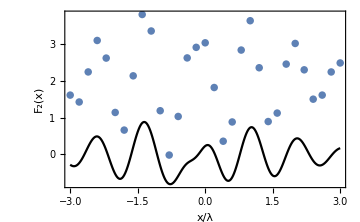

```mathematica
Show[pInt,pSum,PlotRange->All,ImageSize->Medium]
```

Now we compare with the SEM expansion.

```mathematica
pSEM=ListLinePlot[semTab,PlotStyle->Red,AxesLabel->{"x/λ","F_2(x)"},Frame->True,LabelStyle->{FontSize->15}];
```

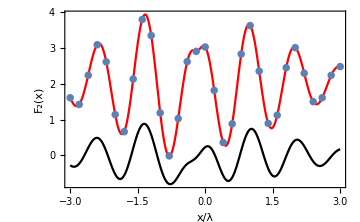

```mathematica
pMeso=Show[pSEM,pSum,pInt,PlotRange->All,ImageSize->Medium]
```

```mathematica
Export["pMeso.pdf",pMeso]
```

pMeso.pdf

## Macroscopic system

Sum computation via SEM is independent of λ. Exact summation on the other hand scales as λ^3,

```mathematica
AbsoluteTiming[NSumSEM[x0+λMeso*a1,λMeso]][[1]]
```

2.76128

```mathematica
AbsoluteTiming[NSumSEM[x0+10000λMeso*a1,10000λMeso]][[1]]
```

1.87835

Hence we can compute even macroscopically large systems.

```mathematica
λMacro=10^5;
```

```mathematica
semTabMacro=ParallelTable[{Norm[a1]i/λMacro,NSumSEM[x0+i*a1,λMacro]},{i,-3/2*λMacro,3/2*λMacro,Ceiling[λMacro/100]}];
```

```mathematica
intTabMacro=ParallelTable[{Norm[a1]*i/λMacro,Length[xVecPy]/Abs[Det[aPy]]*IntNumEpsilon[x0+i*a1,λMacro]},{i,-3/2*λMacro,3/2*λMacro,λMacro/100}];
```

```mathematica
pSEMMacro=ListLinePlot[semTabMacro,PlotStyle->Red,AxesLabel->{"x/λ","F_2(x)"},Frame->True,LabelStyle->{FontSize->15}];
pIntMacro=ListLinePlot[intTabMacro,PlotStyle->Black,AxesLabel->{"x/λ","F_2(x)"},Frame->True,LabelStyle->{FontSize->15}];
```

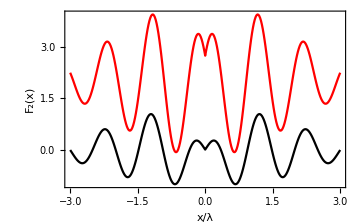

```mathematica
pMacro=Show[pSEMMacro,pIntMacro,PlotRange->All,ImageSize->Medium]
```